Generating the (16, 256, 5) sequential code.

```mathematica
n=16;
d=5;
code={ConstantArray[0,n]};
For[i=0,i<=2^n-1,i++,
v=IntegerDigits[i,2,n];
If[Apply[And,Table[HammingDistance[code[[k]],v]>=d,{k,Length[code]}]],code=Append[code,v]]
]
Length[code]
```

256

Calculating all pairwise Hamming distances between codewords for the code above.

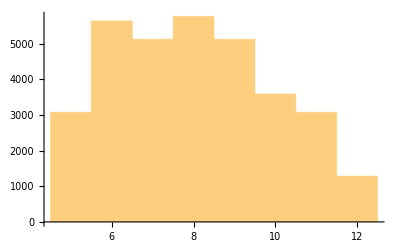

```mathematica
d1={};
For[i=2,i<=Length[code],i++,
For[j=1,j<i,j++,
d1=Append[d1,HammingDistance[code[[i]],code[[j]]]]]
]
Histogram[d1]
```

Generating the Nordstrom Robinson code (15, 256, 5).

```mathematica
x=Tuples[{0,1},8];
code=Table[Join[x[[n]],Table[Mod[x[[n,8]]+x[[n,Mod[i+6,7]+1]]+x[[n,Mod[i,7]+1]]+x[[n,Mod[i+1,7]+1]]+x[[n,Mod[i+3,7]+1]]+(x[[n,Mod[i,7]+1]]+x[[n,Mod[i+4,7]+1]])(x[[n,Mod[i+1,7]+1]]+x[[n,Mod[i+2,7]+1]]+x[[n,Mod[i+3,7]+1]]+x[[n,Mod[i+5,7]+1]])+(x[[n,Mod[i+1,7]+1]]+x[[n,Mod[i+2,7]+1]])(x[[n,Mod[i+3,7]+1]]+x[[n,Mod[i+5,7]+1]]),2],{i,0,6}]],{n,256}];
Length[code]
```

256

Calculating all pairwise Hamming distances between codewords for the Nordstrom Robinson code.

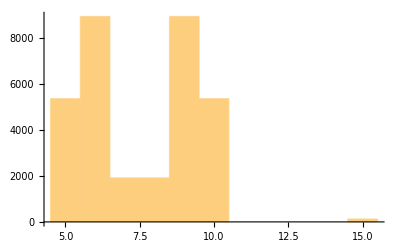

```mathematica
d2={};
For[i=2,i<=Length[code],i++,
For[j=1,j<i,j++,
d2=Append[d2,HammingDistance[code[[i]],code[[j]]]]]
]
Histogram[d2]
```

It is clear that the two codes above are not equivalent since in the Nordstrom Robinson code there are no codewords with Hamming distance of 11, but in the sequential code there are 3,072 pairs of codewords with Hamming distance of 11.

```mathematica
Count[d1,11]
```

3072

Generating the (17, 512, 5) sequential code.

```mathematica
n=17;
d=5;
code={ConstantArray[0,n]};
For[i=0,i<=2^n-1,i++,
v=IntegerDigits[i,2,n];
If[Apply[And,Table[HammingDistance[code[[k]],v]>=d,{k,Length[code]}]],code=Append[code,v]]
]
Length[code]
```

512

Calculating all pairwise Hamming distances between codewords for the  sequential (17, 512, 5) code.

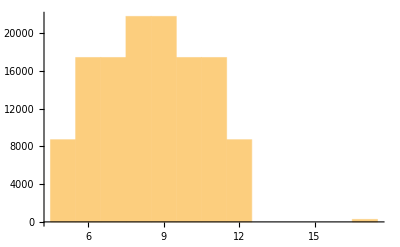

```mathematica
d3={};
For[i=2,i<=Length[code],i++,
For[j=1,j<i,j++,
d3=Append[d3,HammingDistance[code[[i]],code[[j]]]]]
]
Histogram[d3]
```